# Neural Networks

Use a GPU for training, when available:

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

## Multi Layer Neural Networks

#### Training for y = x^2

Here add a nonlinear hyperbolic Tan function, so see how the results improve.

```mathematica
net=NetChain[{
DotPlusLayer[1],
ElementwiseLayer[Tanh]
},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

Create the training data set:

```mathematica
data=Table[x->x^2,{x,RandomReal[1,10000]}];
```

Train with the data set:

```mathematica
result=NetTrain[net,data]
```

NetChain[]

Visually inspect the result.

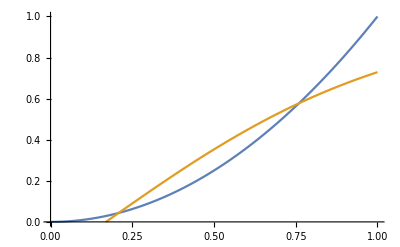

```mathematica
Plot[{x^2,result[x]},{x,0,1},PlotRange->{{0,1},{0,1}}]
```

This result is still rather bad, so next let’s increase the number of nodes to give the neural network more degrees of freedom to work with.

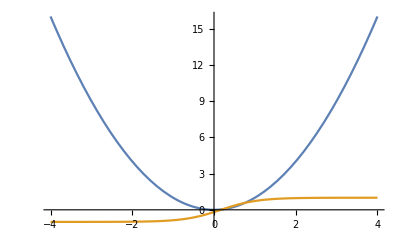

```mathematica
Plot[{x^2,result[x]},{x,-4,4}]
```

#### Training for y = x^2, second attempt

Here we set up a neural network with 10 nodes in the first fully connected layer. Then we use the hyperbolic tan function to introduce a non-linear element. Finally we add one more fully-connected layer to end up with a single scalar output value:

```mathematica
net=NetChain[{
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[1]
},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

Initialize the network:

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
data=Table[x->x^2,{x,RandomReal[1,10000]}];
```

```mathematica
RandomSample[data,5]//Column
```

0.395575→0.15648
0.943356→0.88992
0.958127→0.918008
0.105265→0.0110807
0.677404→0.458876

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->200]
```

NetChain[]

Now let’s take a look at the result (and compare with the expected x^2 result):

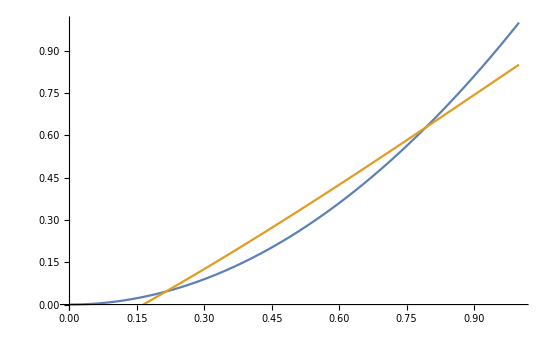

```mathematica
Plot[{x^2,result[x]},{x,0,1},PlotRange->{{0,1},{0,1}}]
```

It’s a little bit better, but still not a great approximation of the x^2 function. Here it is on a larger domain:

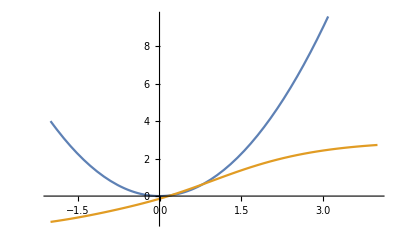

```mathematica
Plot[{x^2,result[x]},{x,-2,4}]
```

#### Training for y = x^2, third attempt: more layers

Let’s try adding two more layers (another fully-connected layer of 4 nodes and another Tanh layer:

```mathematica
net=NetChain[{
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[1]
},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

```mathematica
data=Table[x->x^2,{x,RandomReal[{-1,1},10000]}];
```

```mathematica
RandomSample[data,5]//Column
```

-0.564251→0.318379
-0.998047→0.996099
-0.286815→0.0822627
-0.787554→0.620242
0.899828→0.80969

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->200]
```

NetChain[]

Now the result is much improved. The trained neural network function ‘result’ closely follows the expected x^2 curve:

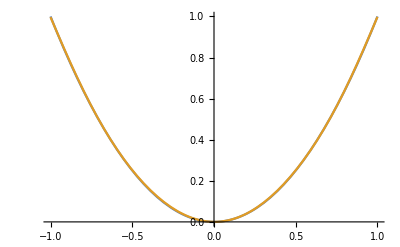

```mathematica
Plot[{x^2,result[x]},{x,-1,1},PlotRange->{{-1,1},{0,1}}]
```

The error:

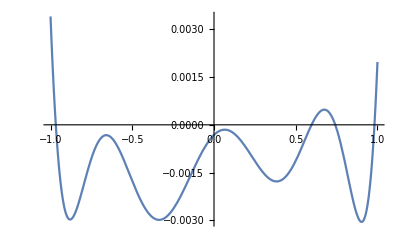

```mathematica
Plot[x^2-result[x],{x,-1,1}]
```

On a wider domain, the trained ‘result’ function still quickly diverges from the expected x^2 function:

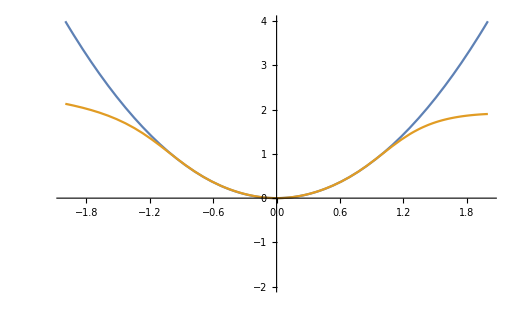

```mathematica
Plot[{x^2,result[x]},{x,-2,2},PlotRange->{{-2,2},{-2,4}}]
```

#### Training for y = x^3-x

Let’s look at one more case, where we look at x^3-x:

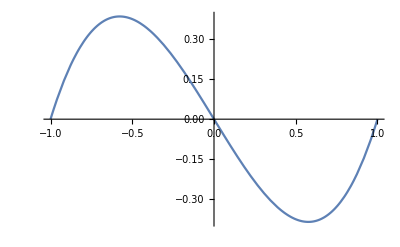

```mathematica
Plot[x^3-x,{x,-1,1}]
```

Define a neural network with multiple layers to use for training:

```mathematica
net=NetChain[{
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[1]
},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

Set up the training data:

```mathematica
data=Table[x->x^3-x,{x,RandomReal[{-1,1},10000]}];
```

```mathematica
RandomSample[data,5]//Column[#,Alignment->"→"]&
```

0.371628→-0.320303
-0.133593→0.131209
0.89957→-0.171614
0.755312→-0.32441
0.0395919→-0.0395299

```mathematica
result=NetTrain[net,data,MaxTrainingRounds->200]
```

NetChain[]

And take a look at the result:

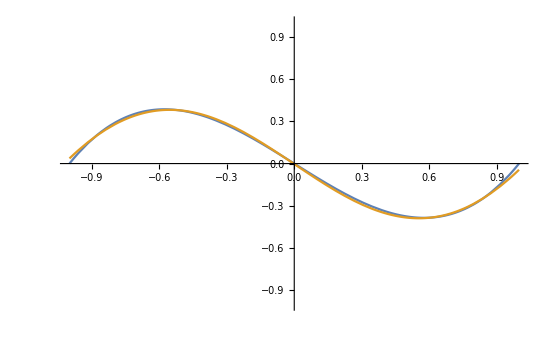

```mathematica
Plot[{x^3-x,result[x]},{x,-1,1},PlotRange->{{-1,1},{-1,1}}]
```

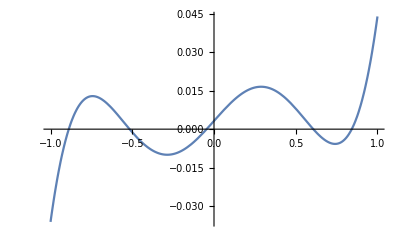

```mathematica
Plot[(x^3-x)-result[x],{x,-1,1}]
```

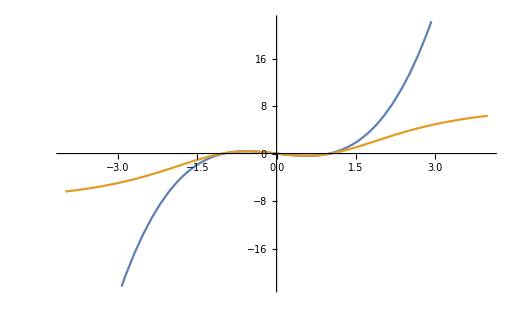

```mathematica
Plot[{x^3-x,result[x]},{x,-4,4}]
```